```mathematica
tc[t_]={t,t^2,t^3}
vel[t_]=D[tc[t],t]
speed[t_]=Sqrt[vel[t].vel[t]]//FullSimplify
acc[t_]=D[vel[t],t]
unittan[t_]= vel[t]/Sqrt[vel[t].vel[t]]
unittanp[t_]=D[unittan[t],t]//FullSimplify
unittanpmag[t_]=Sqrt[unittanp[t].unittanp[t]]
k[t_]=unittanpmag[t]/speed[t]
xvector = {1,0,0}
```

{t,t^2,t^3}

{1,2 t,3 t^2}

√(1+4 t^2+9 t^4)

{0,2,6 t}

{1/(√(1+4 t^2+9 t^4)),(2 t)/(√(1+4 t^2+9 t^4)),(3 t^2)/(√(1+4 t^2+9 t^4))}

{-(2 t (2+9 t^2))/((1+4 t^2+9 t^4)^(3/2)),(2-18 t^4)/((1+4 t^2+9 t^4)^(3/2)),(6 (t+2 t^3))/((1+4 t^2+9 t^4)^(3/2))}

√((4 t^2 (2+9 t^2)^2)/((1+4 t^2+9 t^4)^3)+(36 (t+2 t^3)^2)/((1+4 t^2+9 t^4)^3)+((2-18 t^4)^2)/((1+4 t^2+9 t^4)^3))

(√((4 t^2 (2+9 t^2)^2)/((1+4 t^2+9 t^4)^3)+(36 (t+2 t^3)^2)/((1+4 t^2+9 t^4)^3)+((2-18 t^4)^2)/((1+4 t^2+9 t^4)^3)))/(√(1+4 t^2+9 t^4))

{1,0,0}

```mathematica
Manipulate[
Show [
ParametricPlot3D[tc[t],{t,-3,3}, Axes-> True, AxesOrigin->{0,0,0},Boxed->False,PlotRange->9],
Graphics3D[{PointSize[0.02],Red,Point[tc[q]]}],
Graphics3D[Arrow[{tc[q],tc[q]+vel[q]}]],
Graphics3D[Arrow[{tc[q],tc[q]+unittan[q]}]],
ParametricPlot3D[{tc[q]+vel[q]*t},{t,-1,1},PlotStyle->{Purple,Thickness-> 0.009}]
],
{q,-3,3}
]
```

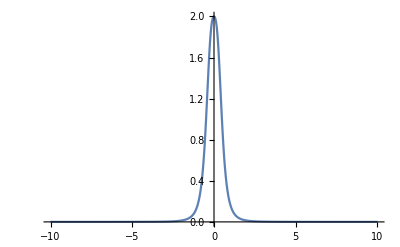

```mathematica
Plot[k[t],{t,-10,10},PlotRange->Full]
```

```mathematica
ParametricPlot3D[{t,t^2,t^3},{t,-2,2}]
```

-Graphics3D-